InterpolatingFunction[…]

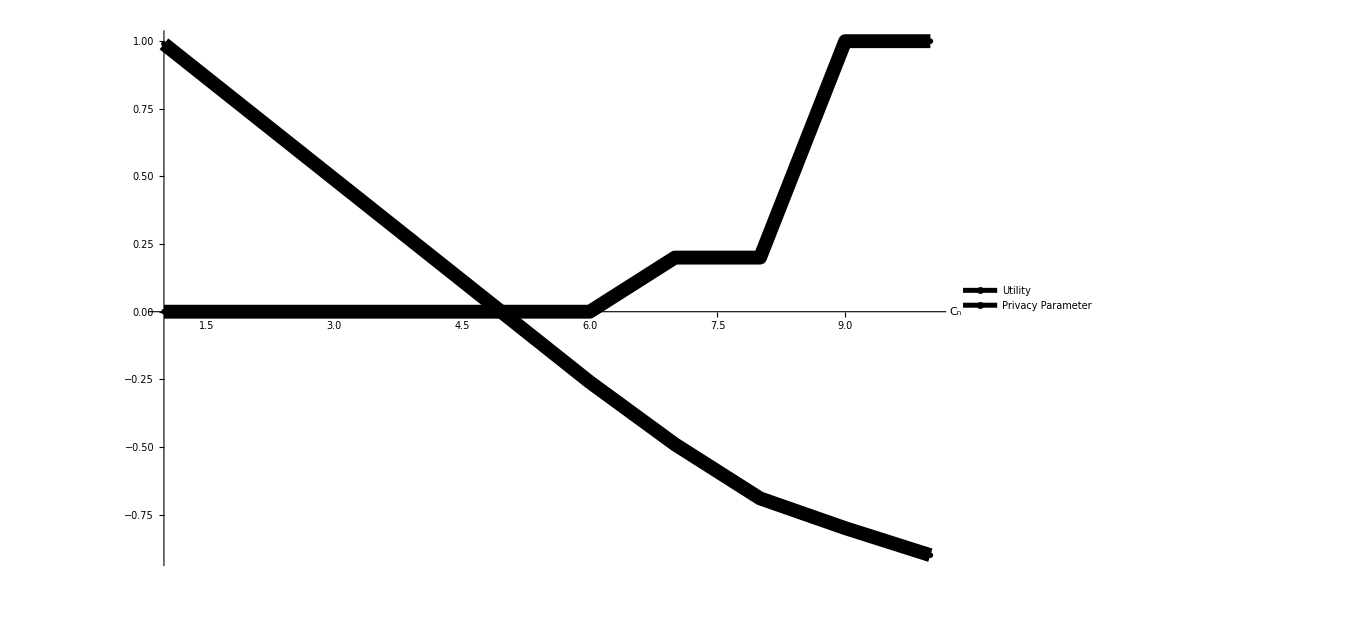

```mathematica
(*CaaS RS M1 Sup*)
iHIDm1=Interpolation[{
{{0,0},0.99},
{{0,0.2},0.79},
{{0,0.4},0.4},
{{0,0.6},0.23},
{{0.2,0},0.71},
{{0.2,0.2},0.37},
{{0.2,0.4},-0.1},
{{0.2,0.6},-0.58},
{{0.4,0},0.27},
{{0.4,0.2},-0.23},
{{0.4,0.4},-0.65},
{{0.4,0.6},-1.23},
{{0.6,0},-0.25},
{{0.6,0.2},-0.88},
{{0.6,0.4},-1.32},
{{0.6,0.6},-1.74}},InterpolationOrder->1]

uHIDi[own_,other_,C_]:=Module[{b,a=iHIDm1[own,other]},
b=Max[0,a]/Null;
b-C *(1-own)]

ListPlot[Transpose[Table[{Maximize[{uHIDi[x,0,c],0≤x≤0.6},x][[1]],If[ArgMax[{uHIDi[x,0,c],0≤x≤0.6},x]==0.6,1,ArgMax[{uHIDi[x,0,c],0≤x≤0.6},x]]},{c,0,2.25,0.25}]],AxesOrigin->{1,0},Joined->True,PlotMarkers->{{-Graphics-,0.05},{-Graphics-,0.05}},PlotStyle->{{Black,Thickness[0.01]},{Black,Thickness[0.01]}},PlotLegends->{Text[Style["Utility",Bold,FontSize->24]], Text[Style["Privacy Parameter",Bold,FontSize->24]]},AxesLabel->{Style["C_n",Bold,Black,FontSize->36],Style["",Bold,Black,FontSize->24]},AxesStyle->Directive[Gray,Thickness[0.005]],TicksStyle->Directive["Label", 24,Bold,Black],ImageSize->1000,PlotRange->Full]
```

InterpolatingFunction[…]

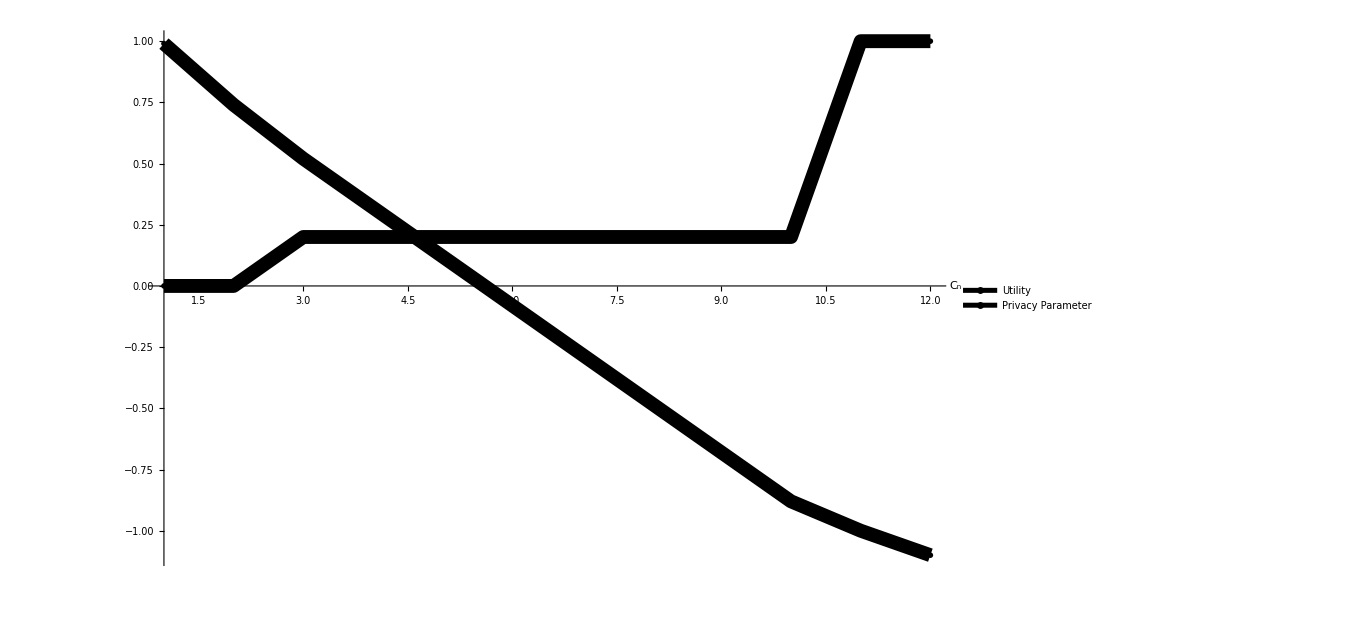

```mathematica
(*CaaS RS M1 bDP*)
ibDPm1=Interpolation[{
{{0,0},0.99},
{{0,0.2},0.93},
{{0,0.4},0.6},
{{0,0.6},-0.11},
{{0.2,0},0.92},
{{0.2,0.2},0.86},
{{0.2,0.4},0.49},
{{0.2,0.6},-0.2},
{{0.4,0},0.08},
{{0.4,0.2},0.06},
{{0.4,0.4},-0.3},
{{0.4,0.6},-1.12},
{{0.6,0},-1.85},
{{0.6,0.2},-1.86},
{{0.6,0.4},-2.34},
{{0.6,0.6},-3.18}},InterpolationOrder->1]

ubDPi[own_,other_,C_]:=Module[{b,a=ibDPm1[own,other]},
b=Max[0,a]/Null;
b-C *(1-own)]

ListPlot[Transpose[Table[{Maximize[{ubDPi[x,0,c],0≤x≤0.6},x][[1]],If[ArgMax[{ubDPi[x,0,c],0≤x≤0.6},x]==0.6,1,ArgMax[{ubDPi[x,0,c],0≤x≤0.6},x]]},{c,0,2.75,0.25}]],AxesOrigin->{1,0},Joined->True,PlotMarkers->{{-Graphics-,0.05},{-Graphics-,0.05}},PlotStyle->{{Black,Thickness[0.01]},{Black,Thickness[0.01]}},PlotLegends->{Text[Style["Utility",Bold,FontSize->24]], Text[Style["Privacy Parameter",Bold,FontSize->24]]},AxesLabel->{Style["C_n",Bold,Black,FontSize->36],Style["",Bold,Black,FontSize->24]},AxesStyle->Directive[Gray,Thickness[0.005]],TicksStyle->Directive["Label", 24,Bold,Black],ImageSize->1000,PlotRange->Full]
```

InterpolatingFunction[…]

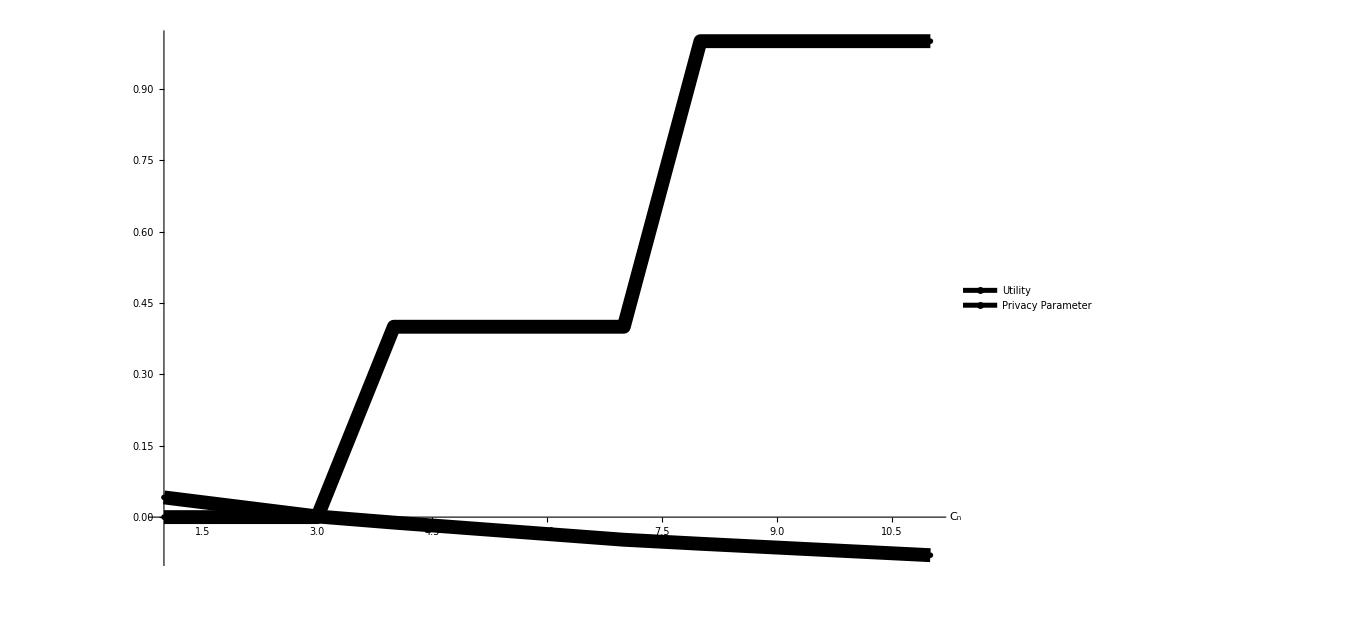

```mathematica
(*CaaS DD Same*)
iHidDD=Interpolation[{
{{0,0},0.041401478},
{{0,0.2},0.033368076},
{{0,0.4},0.024667566},
{{0,0.6},0.012958232},
{{0.2,0},0.033260763},
{{0.2,0.2},0.024456906},
{{0.2,0.4},0.014420283},
{{0.2,0.6},-0.000828438},
{{0.4,0},0.024473382},
{{0.4,0.2},0.014125252},
{{0.4,0.4},-0.000084989},
{{0.4,0.6},-0.019042677},
{{0.6,0},-0.011677678},
{{0.6,0.2},-0.000230962},
{{0.6,0.4},-0.018848678},
{{0.6,0.6},0.040569395}},InterpolationOrder->1]

uHIDiDD[own_,other_,C_]:=Module[{b,a=iHidDD[own,other]},
b=Max[0,a]/Null;
b-C *(1-own)]

ListPlot[Transpose[Table[{Maximize[{uHIDiDD[x,0,c],0≤x≤0.6},x][[1]],If[ArgMax[{uHIDiDD[x,0,c],0≤x≤0.6},x]==0.6,1,ArgMax[{uHIDiDD[x,0,c],0≤x≤0.6},x]]},{c,0,0.2,0.02}]],AxesOrigin->{1,0},Joined->True,PlotMarkers->{{-Graphics-,0.05},{-Graphics-,0.05}},PlotStyle->{{Black,Thickness[0.01]},{Black,Thickness[0.01]}},PlotLegends->{Text[Style["Utility",Bold,FontSize->24]], Text[Style["Privacy Parameter",Bold,FontSize->24]]},AxesLabel->{Style["C_n",Bold,Black,FontSize->36],Style["",Bold,Black,FontSize->24]},AxesStyle->Directive[Gray,Thickness[0.005]],TicksStyle->Directive["Label", 24,Bold,Black],ImageSize->1000,PlotRange->Full]
```

```mathematica
(*Original & Approximated Result: RS M1*)
ibDPApp1=Interpolation[{
{{0,0},0.0028},
{{0,0.2},0.0026},
{{0,0.4},0.0024},
{{0,0.6},-0.0005},
{{0.2,0},0.0025},
{{0.2,0.2},0.0016},
{{0.2,0.4},0.0015},
{{0.2,0.6},-0.0005},
{{0.4,0},-0.0007},
{{0.4,0.2},-0.001},
{{0.4,0.4},-0.0019},
{{0.4,0.6},-0.0037},
{{0.6,0},-0.0101},
{{0.6,0.2},-0.0116},
{{0.6,0.4},-0.0137},
{{0.6,0.6},-0.0174}},InterpolationOrder->1];
ibDPApp2=Interpolation[{
{{0,0},0.0017},
{{0,0.2},0.0016},
{{0,0.4},0.0016},
{{0,0.6},-0.0005},
{{0.2,0},0.0014},
{{0.2,0.2},0.0012},
{{0.2,0.4},0.0012},
{{0.2,0.6},-0.0007},
{{0.4,0},-0.0014},
{{0.4,0.2},-0.0017},
{{0.4,0.4},-0.0028},
{{0.4,0.6},-0.006},
{{0.6,0},-0.0119},
{{0.6,0.2},-0.0121},
{{0.6,0.4},-0.0128},
{{0.6,0.6},-0.0183}},InterpolationOrder->1];
ibDPReal1=Interpolation[{
{{0,0},0.0017},
{{0,0.2},0.0012},
{{0,0.4},0.0011},
{{0,0.6},-0.0003},
{{0.2,0},0.0015},
{{0.2,0.2},0.0014},
{{0.2,0.4},0.0008},
{{0.2,0.6},-0.0026},
{{0.4,0},-0.0013},
{{0.4,0.2},-0.0019},
{{0.4,0.4},-0.0033},
{{0.4,0.6},-0.0069},
{{0.6,0},-0.0116},
{{0.6,0.2},-0.0132},
{{0.6,0.4},-0.0149},
{{0.6,0.6},-0.0208}},InterpolationOrder->1];
ibDPReal2=Interpolation[{
{{0,0},0.0031},
{{0,0.2},0.0023},
{{0,0.4},0.0017},
{{0,0.6},-0.0005},
{{0.2,0},0.0031},
{{0.2,0.2},0.0022},
{{0.2,0.4},0.0011},
{{0.2,0.6},-0.0018},
{{0.4,0},-0.0014},
{{0.4,0.2},-0.0016},
{{0.4,0.4},-0.0022},
{{0.4,0.6},-0.0052},
{{0.6,0},-0.0113},
{{0.6,0.2},-0.0125},
{{0.6,0.4},-0.013},
{{0.6,0.6},-0.0185}},InterpolationOrder->1];

ubDPiApp1[own_,other_,C_]:=Module[{b,a=ibDPApp1[own,other]},
b=100 Max[0,a]/Null;
b-C *(1-own)]
ubDPiApp2[own_,other_,C_]:=Module[{b,a=ibDPApp2[own,other]},
b=100 Max[0,a]/Null;
b-C *(1-own)]
ubDPiReal1[own_,other_,C_]:=Module[{b,a=ibDPReal1[own,other]},
b=100 Max[0,a]/Null;
b-C *(1-own)]
ubDPiReal2[own_,other_,C_]:=Module[{b,a=ibDPReal2[own,other]},
b=100 Max[0,a]/Null;
b-C *(1-own)]
```

```mathematica
(*NE w/ SD: RS M1*)
Module[{prev,actual,succ,finA1,finA2,finR1,finR2,c1=0.1,c2=0.1},
prev={0.0,0.0};
actual={0.0,0.0};
succ={1,1};
While[prev≠succ,
prev=actual;
actual[[1]]=If[ubDPiApp1[actual[[2]],ArgMax[{ubDPiApp1[x,actual[[2]],c1],0≤x≤0.6},x],c1]<0,0.6,ArgMax[{ubDPiApp1[x,actual[[2]],c1],0≤x≤0.6},x]];
actual[[2]]=If[ubDPiApp1[actual[[1]],ArgMax[{ubDPiApp1[x,actual[[1]],c2],0≤x≤0.6},x],c2]<0,0.6,ArgMax[{ubDPiApp1[x,actual[[1]],c2],0≤x≤0.6},x]];
succ=actual];
If[Or[succ[[1]]==0.6,succ[[2]]==0.6],succ[[1]]=1;succ[[2]]=1];
finA1={succ,
If[Or[succ[[1]]==1,succ[[2]]==1],{0,0},{ubDPiApp1[succ[[1]],succ[[2]],c1],ubDPiApp1[succ[[2]],succ[[1]],c1]}],
If[Or[succ[[1]]==1,succ[[2]]==1],1,1-(ibDPApp1[succ[[1]],succ[[2]]]+ibDPApp1[succ[[2]],succ[[1]]])/(2*ibDPApp1[0,0])]};

prev={0.0,0.0};
actual={0.0,0.0};
succ={1,1};
While[prev≠succ,
prev=actual;
actual[[1]]=If[ubDPiApp2[actual[[2]],ArgMax[{ubDPiApp2[x,actual[[2]],c2],0≤x≤0.6},x],c2]<0,0.6,ArgMax[{ubDPiApp2[x,actual[[2]],c2],0≤x≤0.6},x]];
actual[[2]]=If[ubDPiApp2[actual[[1]],ArgMax[{ubDPiApp2[x,actual[[1]],c1],0≤x≤0.6},x],c1]<0,0.6,ArgMax[{ubDPiApp2[x,actual[[1]],c1],0≤x≤0.6},x]];
succ=actual];
If[Or[succ[[1]]==0.6,succ[[2]]==0.6],succ[[1]]=1;succ[[2]]=1];
finA2={succ,
If[Or[succ[[1]]==1,succ[[2]]==1],{0,0},{ubDPiApp2[succ[[1]],succ[[2]],c2],ubDPiApp2[succ[[2]],succ[[1]],c1]}],
If[Or[succ[[1]]==1,succ[[2]]==1],1,1-(ibDPApp2[succ[[1]],succ[[2]]]+ibDPApp2[succ[[2]],succ[[1]]])/(2*ibDPApp2[0,0])]};

prev={0.0,0.0};
actual={0.0,0.0};
succ={1,1};
While[prev≠succ,
prev=actual;
actual[[1]]=If[ubDPiApp1[actual[[2]],ArgMax[{ubDPiReal1[x,actual[[2]],c1],0≤x≤0.6},x],c1]<0,0.6,ArgMax[{ubDPiReal1[x,actual[[2]],c1],0≤x≤0.6},x]];
actual[[2]]=If[ubDPiApp1[actual[[1]],ArgMax[{ubDPiReal1[x,actual[[1]],c2],0≤x≤0.6},x],c2]<0,0.6,ArgMax[{ubDPiReal1[x,actual[[1]],c2],0≤x≤0.6},x]];
succ=actual];
If[Or[succ[[1]]==0.6,succ[[2]]==0.6],succ[[1]]=1;succ[[2]]=1];
finR1={succ,
If[Or[succ[[1]]==1,succ[[2]]==1],{0,0},{ubDPiReal1[succ[[1]],succ[[2]],c1],ubDPiReal1[succ[[2]],succ[[1]],c1]}],
If[Or[succ[[1]]==1,succ[[2]]==1],1,1-(ibDPReal1[succ[[1]],succ[[2]]]+ibDPReal1[succ[[2]],succ[[1]]])/(2*ibDPReal1[0,0])]};

prev={0.0,0.0};
actual={0.0,0.0};
succ={1,1};
While[prev≠succ,
prev=actual;
actual[[1]]=If[ubDPiApp2[actual[[2]],ArgMax[{ubDPiReal2[x,actual[[2]],c2],0≤x≤0.6},x],c2]<0,0.6,ArgMax[{ubDPiReal2[x,actual[[2]],c2],0≤x≤0.6},x]];
actual[[2]]=If[ubDPiApp2[actual[[1]],ArgMax[{ubDPiReal2[x,actual[[1]],c1],0≤x≤0.6},x],c1]<0,0.6,ArgMax[{ubDPiReal2[x,actual[[1]],c1],0≤x≤0.6},x]];
succ=actual];
If[Or[succ[[1]]==0.6,succ[[2]]==0.6],succ[[1]]=1;succ[[2]]=1];
finR2={succ,
If[Or[succ[[1]]==1,succ[[2]]==1],{0,0},{ubDPiReal2[succ[[1]],succ[[2]],c2],ubDPiReal2[succ[[2]],succ[[1]],c1]}],
If[Or[succ[[1]]==1,succ[[2]]==1],1,1-(ibDPReal2[succ[[1]],succ[[2]]]+ibDPReal2[succ[[2]],succ[[1]]])/(2*ibDPReal2[0,0])]};

Print["Approx P1:", finA1];
Print["True P1:", finR1];
Print["Obtained P1:",ubDPiReal1[finA1[[1,1]],finA1[[1,2]],c1]];
Print["Approx P1:", finA2];
Print["True P2:", finR2];
Print["Obtained P2:",ubDPiReal2[finA2[[1,1]],finA2[[1,2]],c2]]]
```

Approx P1:{{0.,0.},{0.18,0.18},0.}

True P1:{{0.2,0.2},{0.06,0.06},0.176471}

Obtained P1:0.07

Approx P1:{{0.,0.},{0.07,0.07},0.}

True P2:{{0.2,0.2},{0.14,0.14},0.290323}

Obtained P2:0.21